```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol "MaTeX" appears in multiple contexts {"MaTeX`", "Global`"}; definitions in context "MaTeX`" may shadow or be shadowed by other definitions.

```mathematica
ConfigureMaTeX[]
```

{CacheSize→100,Ghostscript→/home/cplumber/bin/gs,pdfLaTeX→/local/site/pkg/texlive/2013/bin/x86_64-linux/pdflatex}

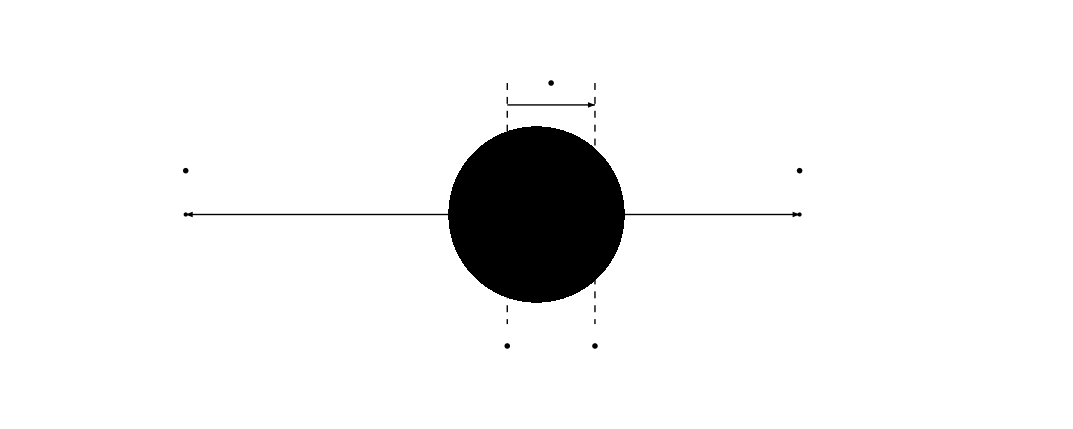

```mathematica
(*Colored noise, opposite directions*)
{p1,p2,p3,p4}={{-4,0},{-1/3,0},{2/3,0},{3,0}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)]/.R->1,{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\sim\\tau_Q",Magnification->2],24],1/2(p2+p3)+{0,3/2}],Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2})],Text[Style[MaTeX["\\tau_1",Magnification->2],24],(p2-{0,3/2})],Text[Style[MaTeX["\\tau_2",Magnification->2],24],(p3-{0,3/2})],{Thick,Arrowheads[{-2*10^-2,2*10^-2}],Arrow[{p2+{0,5/4},p3+{0,5/4}}]},{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]},{Dashed,Line[{p3+{0,3/2},p3-{0,5/4}}]},{Dashed,Line[{p2+{0,3/2},p2-{0,5/4}}]}}}]]
```

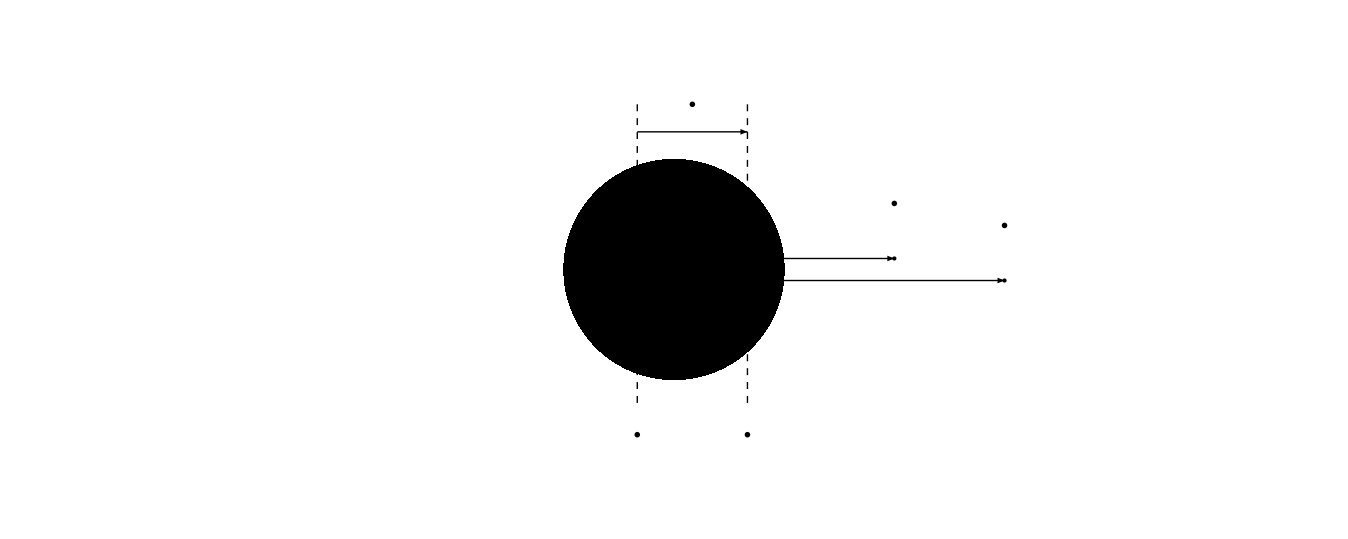

```mathematica
(*Colored noise, same direction*)
{offξ1,offξ2}={1/10,-1/10};
{p1,p2,p3,p4}={{2,offξ1},{-1/3,offξ1},{2/3,offξ2},{3,offξ2}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)]/.R->1,{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\sim\\tau_Q",Magnification->2],24],1/2(p2+p3)+{0,3/2}],Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2})],Text[Style[MaTeX["\\tau_1",Magnification->2],24],(p2-{0,3/2+offξ1})],Text[Style[MaTeX["\\tau_2",Magnification->2],24],(p3-{0,3/2+offξ2})],{Thick,Arrowheads[{-2*10^-2,2*10^-2}],Arrow[{p2+{0,5/4-offξ1},p3+{0,5/4-offξ2}}]},{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]},{Dashed,Line[{p3+{0,3/2+offξ1},p3-{0,5/4-offξ1}}]},{Dashed,Line[{p2+{0,3/2+offξ2},p2-{0,5/4-offξ2}}]}}}]]
```

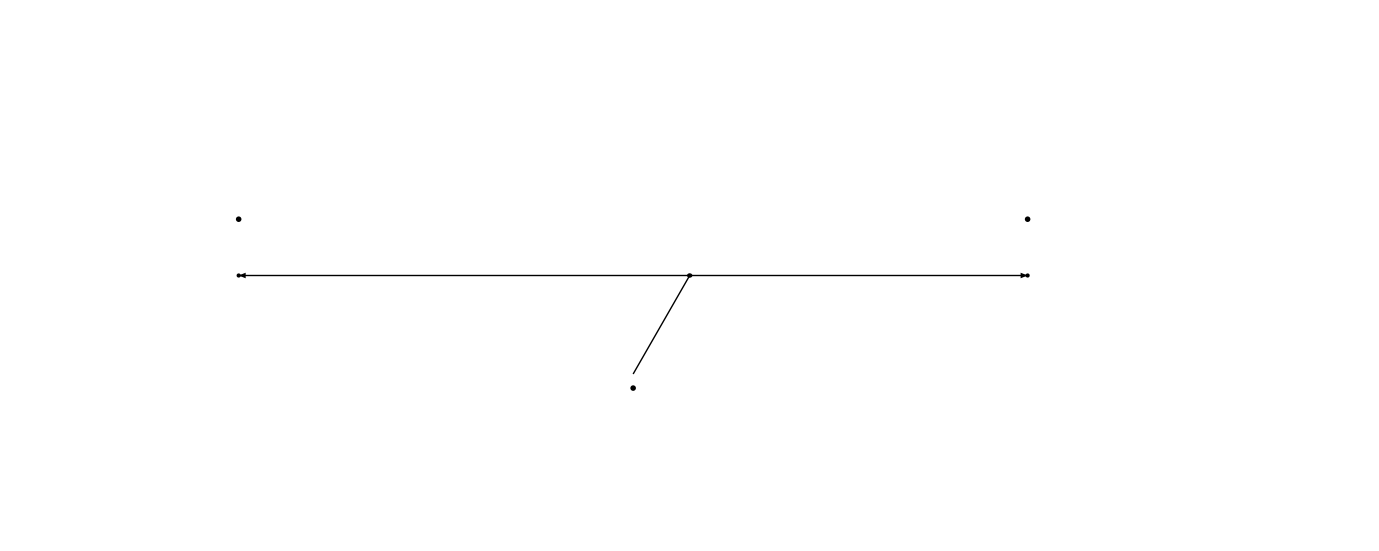

```mathematica
(*White noise, opposite directions*)
R=10^-2;
{p1,p2,p3,p4}={{-4,0},{-R/3,0},{(2R)/3,0},{3,0}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)],{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2})],Text[Style[MaTeX["\\tau_1=\\tau_2",Magnification->2],24],(1/2(p1+p4)-{0,1})],{Line[{1/2(p1+p4)-{0,7/8},1/2(p2+p3)}]},{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]}}}]]
```

```mathematica
(*White noise, same direction*)
R=10^-2;
{offξ1,offξ2}={1/10,-1/10};
{p1,p2,p3,p4}={{2,offξ1},{-R/3,offξ1},{(2R)/3,offξ2},{3,offξ2}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)],{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2-offξ2+offξ1})],Text[Style[MaTeX["\\tau_1",Magnification->2],24],(p2+{0,1/2+0offξ1})],Text[Style[MaTeX["\\tau_2",Magnification->2],24],(p3-{0,1/2+0offξ2})],{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]}}}]]
```

-Graphics-

```mathematica
Triangle[10^-1{{-1/2,-1/(2 √3)},{1/2,-1/(2 √3)},{0,-1/(2 √3)+(√3)/2}}]
```

```mathematica
star[n_,size_,cen_,color_]:=Module[{},
Graphics[{color,Polygon[Riffle[Table[cen+size{Cos[θ],Sin[θ]},{θ,π/2,(5π)/2,(2π)/n}],Table[cen+size/3{Cos[θ],Sin[θ]},{θ,π/2+π/n,(5π)/2+π/n,(2π)/n}]]]}]
];
```

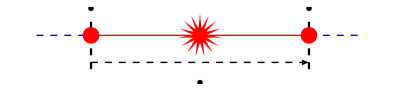

/home/cplumber/CausalChargeDiffusion/CorrelationSourceP1.pdf

```mathematica
Show[
Graphics[{{Dashed,Thickness[0.004],Line[{{-1,-5/16},{-1,2/16}}]},{Dashed,Thickness[0.004],Line[{{1,-5/16},{1,2/16}}]},{Dashed,Thick,Blue,Line[{{-3/2,0},{-1,0}}]},{Dashed,Thick,Blue,Line[{{1,0},{3/2,0}}]},Text[Style[MaTeX["\\xi_1",Magnification->2],24],{-1,1/4}],Text[Style[MaTeX["\\xi_2",Magnification->2],24],{1,1/4}],{PointSize[3 10^-2],Red,Point[{-1,0}]},{PointSize[3 10^-2],Red,Point[{1,0}]},Text[Style[MaTeX["2\\,\\xi_s",Magnification->2],24],{0,-3/8-1/16}],{Dashed,Thick,Arrowheads[{-5*10^-2,5*10^-2}],Arrow[{{-1,-1/4},{1,-1/4}}]},{Arrowheads[{{-5*10^-2,0.25},{5*10^-2,0.75}}],Thick,Red,Arrow[{{-1,0},{1,0}}]}}],star[15,4/2 10^-1,{0,0},Red]]
Export[NotebookDirectory[]<>"CorrelationSourceP1.pdf",%]
```

```mathematica
Show[Graphics[{{Dashed,Thick,Blue,Line[{{-1,0},{-1/2,0}}]},{Dashed,Thick,Blue,Line[{{1/2,0},{1,0}}]},Text[Style[MaTeX["\\xi_1",Magnification->2],24],{-1/2,1/4}],Text[Style[MaTeX["\\xi_2",Magnification->2],24],{1/2,1/4}],{Arrowheads[{{5*10^-2,0.5}}],Thick,Red,Arrow[{{-1/2,1/64},{1/2,1/64}}]},{Arrowheads[{{5*10^-2,0.5}}],Thick,Red,Arrow[{{1/2,-1/64},{-1/2,-1/64}}]},Text[Style[MaTeX["\\xi_s",Magnification->2],24],{0,-3/8}],{Dashed,Thick,Arrowheads[{-5*10^-2,5*10^-2}],Arrow[{{-1/2,-1/4},{1/2,-1/4}}]},{Dashed,Thickness[0.004],Line[{{-1/2,-4/16},{-1/2,2/16}}]},{Dashed,Thickness[0.004],Line[{{1/2,-4/16},{1/2,2/16}}]}}],
star[15,4/4 10^-1,{-1/2,0},Red],star[15,4/4 10^-1,{1/2,0},Red]];
Show[Graphics[{{Dashed,Thick,Blue,Line[{{-3/2,0},{-1/2,0}}]},{Dashed,Thick,Blue,Line[{{1/2,0},{3/2,0}}]},Text[Style[MaTeX["\\xi_1",Magnification->2],24],{-1/2,3/8}],Text[Style[MaTeX["\\xi_2",Magnification->2],24],{1/2,3/8}],{Arrowheads[{{5*10^-2,0.5}}],Thick,Red,Arrow[{{-1/2,1/32},{1/2,1/32}}]},{Arrowheads[{{5*10^-2,0.5}}],Thick,Red,Arrow[{{1/2,-1/32},{-1/2,-1/32}}]},Text[Style[MaTeX["\\xi_s",Magnification->2],24],{0,-7/16}],{Dashed,Thick,Arrowheads[{-5*10^-2,5*10^-2}],Arrow[{{-1/2,-1/4},{1/2,-1/4}}]},{Dashed,Thickness[0.004],Line[{{-1/2,-5/16},{-1/2,4/16}}]},{Dashed,Thickness[0.004],Line[{{1/2,-5/16},{1/2,4/16}}]}}],
star[15,4/2 10^-1,{-1/2,0},Red],star[15,4/2 10^-1,{1/2,0},Red]]
Export[NotebookDirectory[]<>"CorrelationSourceP2.pdf",%]
```

-Graphics-

/home/cplumber/CausalChargeDiffusion/CorrelationSourceP2.pdf

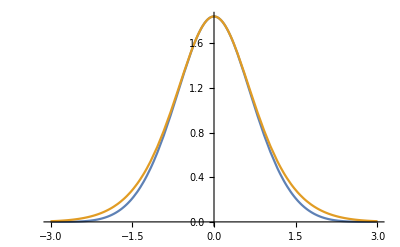

```mathematica
Plot[{Gamma[3,Cosh[x]]/Cosh[x]^2,Gamma[3,(1+1 x^2/2)]/((1+1 x^2/2)^2)},{x,-3,3}]
```

```mathematica
Gamma[3,α Cosh[x]]/Cosh[x]^2//FunctionExpand//Expand
```

ⅇ^(-α Cosh[x]) α^2+2 ⅇ^(-α Cosh[x]) α Sech[x]+2 ⅇ^(-α Cosh[x]) Sech[x]^2

```mathematica
Series[Cosh[x],{x,0,2}]
```

1+x^2/2+O[x]^3

```mathematica
ⅇ^(1/2 (2+x^2) α)Gamma[3,α (1+x^2/2)]/((1+x^2/2)^2)//FunctionExpand//FullSimplify
```

8/((2+x^2)^2)+(4 α)/(2+x^2)+α^2

```mathematica
Integrate[ⅇ^(-1/2 (2+x1^2) α)(8/((2+x1^2)^2)+(4 α)/(2+x1^2)+α^2)ⅇ^(-1/2 (2+x2^2) α)(8/((2+x2^2)^2)+(4 α)/(2+x2^2)+α^2)Exp[-(x1-x2-Δy)^2/w^2],{x1,-∞,∞},{x2,-∞,∞},Assumptions->α>0&&w>0&&Δy>0]
%//FullSimplify
```

Integrate[ⅇ^(-1/2 (4+x1^2+x2^2) α-(-x1+x2+Δy)^2/w^2) (8/((2+x1^2)^2)+(4 α)/(2+x1^2)+α^2) (8/((2+x2^2)^2)+(4 α)/(2+x2^2)+α^2),{x1,-∞,∞},{x2,-∞,∞},Assumptions→α>0&&w>0&&Δy>0]

Integrate[ⅇ^(-1/2 (4+x1^2+x2^2) α-(-x1+x2+Δy)^2/w^2) (8/((2+x1^2)^2)+(4 α)/(2+x1^2)+α^2) (8/((2+x2^2)^2)+(4 α)/(2+x2^2)+α^2),{x1,-∞,∞},{x2,-∞,∞},Assumptions→α>0&&w>0&&Δy>0]

```mathematica
Integrate[(1+2vn Cos[n x])^2 Cos[n x]Exp[-α(1+β Cos[n x])]/.n->2,{x,0,2π},Assumptions->n>0&&n∈Integers]
Integrate[(1+2vn Cos[n x])^2 Cos[n x]Exp[-α(1+β Cos[n x])]/.n->3,{x,0,2π},Assumptions->n>0&&n∈Integers]
Integrate[(1+2vn Cos[n x])^2 Cos[n x]Exp[-α(1+β Cos[n x])]/.n->4,{x,0,2π},Assumptions->n>0&&n∈Integers]
Integrate[(1+2vn Cos[n x])^2 Cos[n x]Exp[-α(1+β Cos[n x])]/.n->5,{x,0,2π},Assumptions->n>0&&n∈Integers]
```

(ⅇ^-α (-2 π (α β+4 vn (-1+vn α β)) BesselI[1,α β]+8 π vn (vn+α β) BesselI[2,α β]))/(α β)

(ⅇ^-α (-2 π (α β+4 vn (-1+vn α β)) BesselI[1,α β]+8 π vn (vn+α β) BesselI[2,α β]))/(α β)

(ⅇ^-α (-2 π (α β+4 vn (-1+vn α β)) BesselI[1,α β]+8 π vn (vn+α β) BesselI[2,α β]))/(α β)

«1 more identical outputs»

```mathematica
Integrate[(1+2vn Cos[2 x])^2 Cos[2 x]Exp[-α-β Cos[2 x]],{x,0,2π}]/Integrate[(1+2vn Cos[2 x])^2 Cos[2 x],{x,0,2π}]//FullSimplify
```

(ⅇ^-α (-(β+4 vn (-1+vn β)) BesselI[1,β]+4 vn (vn+β) BesselI[2,β]))/(2 vn β)

```mathematica
Series[Out[21],{β,0,2}]
```

ⅇ^-α-((ⅇ^-α (1+3 vn^2)) β)/(4 vn)+3/8 ⅇ^-α β^2+O[β]^3

```mathematica
Integrate[(1+2vn Cos[2 x])^2 Cos[2 x],{x,0,2π}]
Integrate[(1+2vn Cos[3 x])^2 Cos[3 x],{x,0,2π}]
```

4 π vn

4 π vn